# Population (Epi) genetics

## Constant Population Size

## Haploid

### Model

```mathematica
(*Selection*)
pas = pa wa;
pAs = pA wA ;
pBs = pB wB;
pbs = pb wb;
(*Mutation*)
pamut = pas (1-μ)(1-ma) + μ pAs +(1-ν)ta pbs ;
pAmut = pAs (1-μ)(1-mA) + μ pas +(1-ν)tA pBs;
pBmut = pBs (1-ν)(1-tA) + (1-μ)mA pAs + ν pbs;
pbmut = pbs (1-ν)(1-ta) + (1-μ)ma pas + ν pBs;
(*Normalization*)
wavg = pamut + pAmut + pBmut + pbmut; 
panext = pamut/wavg;
pAnext = pAmut/wavg;
pBnext = pBmut/wavg; 
pbnext = pbmut/wavg;
recursions = {panext, pAnext, pBnext}/.pb->1-pa-pA-pB;
```

### The QEE (Quasi Epigenetic Equilibrium)

```mathematica
Fitness = {wB->1+sB,wA->1+sA,wa->1+sa,wb->1+sb};
SSWMApprox = {sB->sB ϵ, sA->sA ϵ, sa->sa ϵ, sb->sb ϵ,μ->μ ϵ^2,ν->ν ϵ^2,paef->1-pAef};
ChangeOfVariable = {pA->(1-fB)pAef,pB->fB pAef, pa->(1-fb)(1-pAef),pb->fb (1-pAef)};

fBnext =pBnext/(pAef) //FullSimplify;
%/.ChangeOfVariable//FullSimplify;
Solve[%-fB==0,fB]//FullSimplify;
FullSimplify[fB/.%[[1]],Assumptions->{mA+tA>0,ma+ta>0,μ>0,ν>0,pAef>0}]
%/.Fitness/.SSWMApprox;
FullSimplify[Series[%,{ϵ,0,1}],Assumptions->{mA+tA>0,ma+ta>0,μ>0,ν>0,pAef>0}]
```

1/(2 pAef (wA-wB))((-1+fb) (-1+pAef) wa+mA wA+pAef wA+fb wb-fb pAef wb-wB+tA wB-mA wA μ+wB ν-tA wB ν-√(4 (wA-wB) (mA pAef wA (-1+μ)+fb (-1+pAef) wb ν)+((-1+fb) (-1+pAef) wa+fb wb+pAef (wA-fb wb)+mA (wA-wA μ)+wB (-1+tA+ν-tA ν))^2))

mA/(mA+tA)+(mA (-mA (-1+pAef) ((-1+fb) sa-fb sb+sB)+((-1+fb+pAef-fb pAef) sa-pAef sA+fb (-1+pAef) sb+mA (sA-sB)+sB) tA+(sA-sB) tA^2) ϵ)/(mA+tA)^3+O[ϵ]^2

### General case

```mathematica
pAefnext = pAnext+pBnext/.ChangeOfVariable//FullSimplify;
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->pAef0 + pAef1 ϵ},{ϵ,0,2}]//FullSimplify;
pAef0sol =Solve[Coefficient[DiffSeries, ϵ,1]==0,pAef0]
Coefficient[DiffSeries, ϵ,2]/.pAef0sol[[1]]//FullSimplify;
Solve[%==0,pAef1]//FullSimplify
Coefficient[DiffSeries, ϵ,2]/.pAef0sol[[2]]//FullSimplify;
Solve[%==0,pAef1]//FullSimplify
```

{{pAef0→0},{pAef0→1}}

{{pAef1→(μ-fb μ+fb ν)/(sa-fb sa+(-1+fB) sA+fb sb-fB sB)}}

{{pAef1→(μ-fB μ+fB ν)/(sa-fb sa+(-1+fB) sA+fb sb-fB sB)}}

#### The two equilibrium for p_A are therefore, μ_a_ef/(saeff-sAeff)+O(ϵ^2) and 1-μ_A_ef/(sAeff-saeff)+O(ϵ^2).

## Diploid - Epimutation

### Model

```mathematica
(*Selection*)
pas = pa (pA wAa +pa waa + pB waB + pb wab);
pAs = pA (pA wAA +pa wAa + pB wAB + pb wAb);
pBs = pB (pA wAB +pa waB + pB wBB + pb wBb);
pbs = pb (pA wAb +pa wab + pB wBb + pb wbb);
(*Mutation*)
pamut = pas (1-μ)(1-ma) + μ pAs +(1-ν)ta pbs ;
pAmut = pAs (1-μ)(1-mA) + μ pas +(1-ν)tA pBs;
pBmut = pBs (1-ν)(1-tA) + (1-μ)mA pAs + ν pbs;
pbmut = pbs (1-ν)(1-ta) + (1-μ)ma pas + ν pBs;
(*Normalization*)
wavg = pamut + pAmut + pBmut + pbmut; 
panext = pamut/wavg;
pAnext = pAmut/wavg;
pBnext = pBmut/wavg; 
pbnext = pbmut/wavg;
recursions = {panext, pAnext, pBnext}/.pb->1-pa-pA-pB;
```

### The QEE

```mathematica
Fitness = {wAA->1+sAA,wAa->1+sAa,waa->1+saa,wBB->1+sBB,wBb->1+sBb,wbb->1+sbb,wAB->1+sAB,wAb->1+sAb,waB->1+saB,wab->1+sab}; 
SSWMApprox = {sAA->sAA ϵ,sAa->sAa ϵ,saa->saa ϵ,sBB->sBB ϵ,sBb->sBb ϵ,sbb->sbb ϵ,sAB->sAB ϵ,sAb->sAb ϵ,saB->saB ϵ,sab->sab ϵ,μ->μ ϵ^2, ν->ν ϵ^2}; 
ChangeOfVariable = {pA->(1-fB)pAef,pB->fB pAef, pa->(1-fb)(1-pAef),pb->fb (1-pAef)};
EffectiveFitness = {sAA->(sAAeff-(2 fB (1-fB)sAB + fB^2 sBB))/(1-fB)^2,saa->(saaeff-(2 fb (1-fb)sab + fb^2 sbb ))/(1-fb)^2, sBb->(sAaeff -((1-fB)(1-fb)sAa + (1-fB)fb sAb + fB(1-fb)saB))/(fB fb)};
```

```mathematica
fBnext =pBnext/(pAef) //FullSimplify;
%/.ChangeOfVariable//FullSimplify;
fBDiffSeries = Series[%-fB/.Fitness/.SSWMApprox/.{fB->fB0+fB1 ϵ},{ϵ,0,1}]//FullSimplify;
Solve[Coefficient[fBDiffSeries,ϵ,0]==0,fB0]//FullSimplify
Coefficient[fBDiffSeries,ϵ,1]/.%[[1]];
Solve[%==0,fB1]//FullSimplify;
```

{{fB0→mA/(mA+tA)}}

### Distinct Effective Fitness

```mathematica
pAefnext = pAnext+pBnext/.ChangeOfVariable//FullSimplify;
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->pAef0 +pAef1 ϵ },{ϵ,0,1}]/.EffectiveFitness//FullSimplify;
pAef0sol =Solve[Coefficient[DiffSeries, ϵ,1]==0,pAef0];
pAef0sol=pAef0/.pAef0sol//FullSimplify
```

{0,1,(saaeff-sAaeff)/(saaeff-2 sAaeff+sAAeff)}

#### Since the first order term turns out be zero we now derive the second order term for pAef0 = 0,1.

```mathematica
pAefnext = pAnext+pBnext/.ChangeOfVariable//FullSimplify;
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->pAef1 ϵ },{ϵ,0,2}]/.EffectiveFitness//FullSimplify;
Coefficient[DiffSeries, ϵ,2]/.pAef0->pAef0sol[[1]];
pAef1sol0 =Solve[%==0,pAef1]//FullSimplify;
Numerator[pAef1/.pAef1sol0];
Denominator[pAef1/.pAef1sol0]//FullSimplify;
%%/%
```

{(μ-fb μ+fb ν)/(saaeff-sAaeff)}

#### Note the numerator can be separated in two terms, (1-fb)μ + fb ν, which is μ_a_ef. Therefore we can split pAef2 as μ_a_ef/(saaeff-sAaeff)+O(ϵ^2).

```mathematica
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->1+pAef1 ϵ +pAef2 ϵ^2},{ϵ,0,3}]/.EffectiveFitness//FullSimplify;
Coefficient[DiffSeries, ϵ,2]/.pAef0->pAef0sol[[1]];
pAef1sol0 =Solve[%==0,pAef1]//FullSimplify;
Numerator[pAef1/.pAef1sol0];
Denominator[pAef1/.pAef1sol0]//FullSimplify;
%%/%
Coefficient[DiffSeries, ϵ,3]/.pAef0->pAef0sol[[1]]/.pAef0pAef1->(μ-fB μ+fB ν)/(sAaeff-sAAeff)
pAef1sol0 =Solve[%==0,pAef2]//FullSimplify;
%/.pAef1->(μ-fB μ+fB ν)/(sAaeff-sAAeff)/.EffectiveFitness/.μ->ν//FullSimplify
```

{(μ-fB μ+fB ν)/(sAaeff-sAAeff)}

pAef2 (sAaeff-sAAeff)-pAef1^2 (saaeff-3 sAaeff+2 sAAeff)-fB (sAAeff+(-1+fB) sAB-fB sBB) (μ-ν)+pAef1 (-sAaeff sAAeff+sAAeff^2+(-2+fb+fB) μ-(fb+fB) ν)

{{pAef2→(ν ((sAaeff-sAAeff)^2 sAAeff+(saaeff-sAaeff) ν))/(sAaeff-sAAeff)^3}}

#### As in the previous case we can write this as -μ_A_ef/(sAAeff-sAaeff)+O(ϵ^2).

#### This gives us the three equilibrium for p_A, which are μ_a_ef/(saaeff-sAaeff)+O(ϵ^2), 1- μ_A_ef/(sAAeff-sAaeff)+O(ϵ^2) and (saaeff-sAaeff)/(saaeff - 2sAaeff+sAAeff)+O(ϵ)

### Effective Recessive mutant

#### We now consider the scenarios where effective fitness of atleast a pair is .

#### Case : sAAeff = sAaeff

```mathematica
pAefnext = pAnext+pBnext/.ChangeOfVariable//FullSimplify;
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->pAef0 +pAef1 ϵ^(1/2) },{ϵ,0,2}]/.EffectiveFitness/.sAaeff->sAAeff//FullSimplify;
pAef0sol =Solve[Coefficient[DiffSeries, ϵ,1]==0,pAef0];
pAef0sol=pAef0/.pAef0sol//FullSimplify
```

{0,1,1}

```mathematica
Coefficient[DiffSeries, ϵ,2]/.pAef0->pAef0sol[[2]];
pAef1sol0 =Solve[%==0,pAef1]//FullSimplify;
Numerator[pAef1/.pAef1sol0];
Denominator[pAef1/.pAef1sol0]//FullSimplify;
%%/%
```

{-(√(μ-fB μ+fB ν))/(√(-saaeff+sAAeff)),(√(μ-fB μ+fB ν))/(√(-saaeff+sAAeff))}

#### The equilibrium is given by 1-√(μ_A_ef/(sAAeff-saaeff)), which would be stable when sAAeff = sAaeff > saaeff

#### Case : sAAeff < sAaeff = saaeff

```mathematica
pAefnext = pAnext+pBnext/.ChangeOfVariable//FullSimplify;
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->pAef0 +pAef1 ϵ^(1/2) },{ϵ,0,2}]/.EffectiveFitness/.sAaeff->saaeff//FullSimplify;
pAef0sol =Solve[Coefficient[DiffSeries, ϵ,1]==0,pAef0];
pAef0sol=pAef0/.pAef0sol//FullSimplify
```

{0,0,1}

```mathematica
Coefficient[DiffSeries, ϵ,2]/.pAef0->pAef0sol[[2]];
pAef1sol0 =Solve[%==0,pAef1]//FullSimplify;
Numerator[pAef1/.pAef1sol0];
Denominator[pAef1/.pAef1sol0]//FullSimplify;
%%/%
```

{-(√(μ-fb μ+fb ν))/(√(saaeff-sAAeff)),(√(μ-fb μ+fb ν))/(√(saaeff-sAAeff))}

#### The equilibrium is given by √(μ_a_ef/(saaeff-sAAeff)) which is stable when sAAeff < sAaeff = saeff

#### Case : sAAeff = saaeff = sAaeff

```mathematica
pAefnext = pAnext+pBnext/.ChangeOfVariable//FullSimplify;
DiffSeries =Series[pAefnext-pAef/.Fitness/.SSWMApprox/.{pAef->pAef0 +pAef1 ϵ^(1/2) },{ϵ,0,2}]/.EffectiveFitness/.sAaeff->sAAeff/.saaeff->sAAeff//FullSimplify;
pAef0sol =Solve[Coefficient[DiffSeries, ϵ,2]==0,pAef0];
pAef0sol=pAef0/.pAef0sol//FullSimplify
```

{((-1+fb) μ-fb ν)/((-2+fb+fB) μ-(fb+fB) ν)}

#### The equilibrium is then given by μ_a_ef/(μ_A_ef+μ_a_ef)

#### To summarize p̂A is given by 1- μ_A_ef/(sAAeff-sAaeff)+O(ϵ^2) when sAAeff > sAaeff ; 1-√(μ_A_ef/(sAAeff-saaeff)) + O(ϵ) when sAAeff = sAaeff > saaeff ; μ_a_ef/(saaeff-sAaeff)+O(ϵ^2), when sAAeff < sAaeff < saaeff ; √(μ_a_ef/(saaeff-sAAeff)) + O(ϵ) when sAAeff < sAaeff = saaeff ; (saaeff-sAaeff)/(saaeff - 2sAaeff+sAAeff)+O(ϵ), when sAAeff < sAaeff > saaeff ; μ_a_ef/(μ_a_ef+μ_A_ef)+ O(ϵ) when sAAeff = sAaeff = saaeff ;

#### Note there while the conditions satisfy local stability, it should be noted that there are equilibria that share common locally stable regimes, where the equilibrium is decided by the starting condition p_(A,0) = 1. For instance, μ_a_ef/(saaeff-sAaeff)+O(ϵ^2) is locally stable even when sAAeff > sAaeff < saaeff along with 1- μ_A_ef/(sAAeff-sAaeff)+O(ϵ^2) but the later will be attained first starting with p_(A,0)=1.

## Diploid - Paramutation

```mathematica
Clear[pa,pA]
```

### Paramutagenic Wildtype/Paramutable Mutant - A,a and b

#### Model

```mathematica
(*Selection*)
pas = pa (pA wAa +pa waa + pb wab);
pAs = pA (pA wAA +pa wAa + pb wAb);
pbs = pb (pA wAb +pa wab + pb wbb);
(*Mutation*)
pamut = pas (1-μ)-ma (1-μ)(pA wAa+pb wab)pa + μ pAs +(1-ν)ta pbs ;
pAmut = pAs (1-μ) + μ pas+ν pbs ;
pbmut = pbs (1-ν)(1-ta) + (1-μ)ma (pA wAa+pb wab)pa  ;
(*Normalization*)
wavg = pamut + pAmut + pbmut; 
panext = pamut/wavg;
pAnext = pAmut/wavg; 
pbnext = pbmut/wavg;
```

```mathematica
Fitness = {wAA->1+sAA,wAa->1+sAa,waa->1+saa,wbb->1+sbb,wAb->1+sAb,wab->1+sab}; 
SSWMApprox = {sAA->sAA ϵ,sAa->sAa ϵ,saa->saa ϵ,sBB->sBB ϵ,sBb->sBb ϵ,sbb->sbb ϵ,sAB->sAB ϵ,sAb->sAb ϵ,saB->saB ϵ,sab->sab ϵ,μ->μ ϵ^2, ν->ν ϵ^2,s->s ϵ}; 
ChangeOfVariable = {pA->1-paef, pa->fa paef,pb->(1-fa) paef};
EffectiveFitness = {saa->(saaeff-(2 OverTilde[ma] (1-OverTilde[ma] )sab + OverTilde[ma]^2 sbb ))/(1-OverTilde[ma] )^2, sAb->(sAaeff -(1-OverTilde[ma] )sAa )/OverTilde[ma]  };
```

#### The QEE

```mathematica
fanext = panext/paef//FullSimplify;
%/.ChangeOfVariable//FullSimplify
faDiffSeries = Series[%-fa/.Fitness/.SSWMApprox/.{fa->fa0+fa1 ϵ},{ϵ,0,0}]//FullSimplify
fa0sol=Solve[Coefficient[faDiffSeries,ϵ,0]==0,fa0]//FullSimplify;
(Numerator[fa0/.fa0sol])/(ma+ta)/.{ma->OverTilde[ma](ma+ta),ta->(1-OverTilde[ma])(ma+ta)};
fa0solsim=FullSimplify[%,Assumptions->{ma+ta>0}]/(2 OverTilde[ma] paef)
fa0solSeries = Series[%[[1]]/.{paef -> paef ϵ},{ϵ,0,0}]//Normal
```

(fa (1-paef) paef wAa (1+ma (-1+μ))+(-1+paef)^2 wAA μ+fa^2 paef^2 (waa-waa μ)+(-1+fa) fa paef^2 wab (-1+ma+μ-ma μ+ta (-1+ν))-(-1+fa)^2 paef^2 ta wbb (-1+ν)+(1-fa) (1-paef) paef wAb (ta+μ-ta ν))/(paef (wAA+paef (-2 wAA+2 wAb+2 fa (wAa-paef wAa-wAb+paef (wab+wAb-wbb))+fa^2 paef (waa-2 wab+wbb)+paef (wAA-2 wAb+wbb))))

(fa0^2 ma paef+ta-fa0 (ma+ta))+O[ϵ]^1

{(1-√(1+4 paef (-1+OverTilde[ma]) OverTilde[ma]))/(2 paef OverTilde[ma]),(1+√(1+4 paef (-1+OverTilde[ma]) OverTilde[ma]))/(2 paef OverTilde[ma])}

1-OverTilde[ma]

#### Case 1 : Epigenetically modified allele has the same fitness’ as the other genetic allele.

```mathematica
Case1Assump= {sbb->sAA, sAb->sAA, sab->sAa};
Case1Fitness = {sAA->0,sAa-> -h s, saa-> -s};
```

Case 1a: h ≠ 0 (Non-recessive mutant)

```mathematica
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef0+paef1 ϵ + paef2 ϵ^2+paef3 ϵ^3}/.SSWMApprox,{ϵ,0,3}]//FullSimplify;
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,1]==0,paef0],Assumptions->{0<OverTilde[ma]<1}]/.EffectiveFitness//FullSimplify;
Coefficient[pAdiffSeries,ϵ,2]/.paef0->0//FullSimplify;
Solve[%==0,paef1]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef0->0/.%[[1]]//FullSimplify;
Solve[%==0,paef2]/.EffectiveFitness//FullSimplify
```

{{paef1→μ/(h s-h s OverTilde[ma])}}

{{paef2→-(μ (μ-h μ+((-1+h) μ+h ν) OverTilde[ma]))/(h^3 s^2 (-1+OverTilde[ma])^2)}}

Stability Analysis

```mathematica
D[-pAdiff,paef]//FullSimplify;
Series[%/.fa->fa0solSeries/.paef ->μ/(h s-h s OverTilde[ma])-(μ (μ-h μ+((-1+h) μ+h ν) OverTilde[ma]))/(h^3 s^2 (-1+OverTilde[ma])^2)/.SSWMApprox/.OverTilde[ma]->1-OverTilde[ta] ,{ϵ,0,2}]
```

-h s OverTilde[ta] ϵ+(μ-ν-μ OverTilde[ta]-((2-4 h) μ OverTilde[ta])/h+ν OverTilde[ta]) ϵ^2+O[ϵ]^3

```mathematica
D[-pAdiff,paef]//FullSimplify;
Series[%/.fa->fa0solSeries/.paef ->μ/(h s-h s OverTilde[ma])-(μ (μ-h μ+((-1+h) μ+h ν) OverTilde[ma]))/(h^3 s^2 (-1+OverTilde[ma])^2)/.SSWMApprox/.OverTilde[ma]->1-OverTilde[ta] /.OverTilde[ta] ->OverTilde[ta] ϵ,{ϵ,0,2}]
%//Normal
%/.ϵ->1//FullSimplify
```

(-μ-ν+h s OverTilde[ta] (-1+(2 μ (-ν+h s OverTilde[ta]))/(h^2 s^2 OverTilde[ta]^2))) ϵ^2+O[ϵ]^3

ϵ^2 (-μ-ν+h s OverTilde[ta] (-1+(2 μ (-ν+h s OverTilde[ta]))/(h^2 s^2 OverTilde[ta]^2)))

μ-ν-(2 μ ν)/(h s OverTilde[ta])-h s OverTilde[ta]

```mathematica
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef0+paef1 ϵ + paef2 ϵ^2}/.OverTilde[ma]->1-OverTilde[ta] ϵ/.SSWMApprox,{ϵ,0,3}]//FullSimplify;
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,2]==0,paef0],Assumptions->{0<OverTilde[ma]<1}]/.EffectiveFitness//FullSimplify
(*Coefficient[pAdiffSeries,ϵ,3]//FullSimplify;
Solve[%==0,paef1]/.EffectiveFitness//FullSimplify
(*Coefficient[pAdiffSeries,ϵ,4]/.paef0->μ/(μ+ν)/.%[[1]]//FullSimplify;
Solve[%==0,paef2]/.EffectiveFitness//FullSimplify*)*)
```

{{paef0→(μ+ν+h s OverTilde[ta]-√(-4 h s μ OverTilde[ta]+(μ+ν+h s OverTilde[ta])^2))/(2 h s OverTilde[ta])},{paef0→(μ+ν+h s OverTilde[ta]+√(-4 h s μ OverTilde[ta]+(μ+ν+h s OverTilde[ta])^2))/(2 h s OverTilde[ta])}}

```mathematica
D[-pAdiff,paef]//FullSimplify;
FullSimplify[Series[%/.fa->fa0solSeries/.paef ->(μ+ν+h s OverTilde[ta]-√(-4 h s μ OverTilde[ta]+(μ+ν+h s OverTilde[ta])^2))/(2 h s OverTilde[ta])/.OverTilde[ma]->1- OverTilde[ta]/.OverTilde[ta]->OverTilde[ta] ϵ/.SSWMApprox,{ϵ,0,2}],Assumptions->{h>0,s>0, OverTilde[ta]>0, ϵ>0}]
```

-√((μ+ν)^2+h s OverTilde[ta] (-2 μ+2 ν+h s OverTilde[ta])) ϵ^2+O[ϵ]^3

The equilibrium is given by  μ/(h s OverTilde[ta])-(μ ( μ (1-h)OverTilde[ta] + ν h OverTilde[ma]))/(h^3 s^2 OverTilde[ta]^2)+O(ϵ^3) when OverTilde[ta] > O(ϵ) (roughly when OverTilde[ta]≥ μ/(h s)) and 1/OverTilde[ta](μ+ν)/(2 h s)+1/2-√((1/OverTilde[ta](μ+ν)/(2 h s)+1/2)^2-1/OverTilde[ta]μ/(h s)) otherwise.

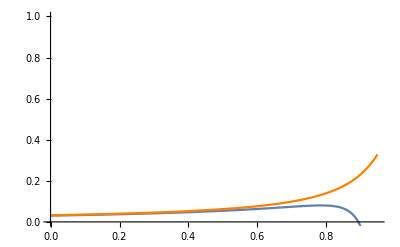

```mathematica
A = Plot[μ/(h s (1-OverTilde[ma]))-((μ(1-h)+h ν OverTilde[ma])μ)/(h^3 s^2(1-OverTilde[ma])^2)/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[ma],0,1}];
B= Plot[(μ+ν+h s OverTilde[ta]-√(-4 h s μ OverTilde[ta]+(μ+ν+h s OverTilde[ta])^2))/(2 h s OverTilde[ta])/.OverTilde[ta]->1-OverTilde[ma]/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[ma],0,1},PlotStyle->{Orange}];

Show[A,B, PlotRange->{0,1}]
```

Case 1b: h = 0 (Recessive mutant)

```mathematica
Case1Assump= {sbb->sAA, sAb->sAA, sab->sAa};
Case1Fitness = {sAA->0,sAa->0, saa-> -s}
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef0+paef1 ϵ^(1/2) + paef2 ϵ+paef3 ϵ^(3/2)}/.SSWMApprox,{ϵ,0,3}]//FullSimplify;
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,3/2]==0,paef0],Assumptions->{0<OverTilde[ma]<1}]/.EffectiveFitness//FullSimplify;
Coefficient[pAdiffSeries,ϵ,2]/.paef0->0//FullSimplify;
Solve[%==0,paef1]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,5/2]/.paef0->0/.%[[2]]//FullSimplify;
Solve[%==0,paef2]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef0->0/.%%%[[2]]/.%[[1]]//FullSimplify;
Solve[%==0,paef3]/.EffectiveFitness//FullSimplify
```

{sAA→0,sAa→0,saa→-s}

{{paef1→-(√μ)/(√(s (-1+OverTilde[ma])^2))},{paef1→(√μ)/(√(s (-1+OverTilde[ma])^2))}}

{{paef2→-(μ+(-μ+ν) OverTilde[ma])/(2 s (-1+OverTilde[ma])^2)}}

{{paef3→((-μ+(μ-ν) OverTilde[ma]) (3 μ+(μ-ν) OverTilde[ma]))/(8 √μ (s (-1+OverTilde[ma])^2)^(3/2))}}

```mathematica
D[-pAdiff,paef]//FullSimplify;
FullSimplify[Series[%/.fa->fa0solSeries/.paef ->(√μ)/(√(s (1-OverTilde[ma])^2))-(μ+(-μ+ν) OverTilde[ma])/(2 s (1-OverTilde[ma])^2)/.SSWMApprox,{ϵ,0,2}],Assumptions->{h>0,s>0, 1>OverTilde[ma]>0,ϵ>0}]
```

2 √(s μ) (-1+OverTilde[ma]) ϵ^(3/2)+2 μ ϵ^2+O[ϵ]^(5/2)

```mathematica
Case1Assump= {sbb->sAA, sAb->sAA, sab->sAa};
Case1Fitness = {sAA->0,sAa->0, saa-> -s}
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef0+paef1 ϵ^(1/2) + paef2 ϵ+paef3 ϵ^(3/2)+paef4 ϵ^2}/.OverTilde[ma]->1-OverTilde[ta] ϵ/.SSWMApprox,{ϵ,0,4}]//FullSimplify
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,2]==0,paef0],Assumptions->{0<OverTilde[ma]<1}]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,5/2]/.paef0->μ/(μ+ν)//FullSimplify;
Solve[%==0,paef1]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef0->μ/(μ+ν)/.%[[1]]//FullSimplify;
Solve[%==0,paef2]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,7/2]/.paef0->μ/(μ+ν)/.%%%[[1]]/.%[[1]]//FullSimplify;
Solve[%==0,paef3]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,4]/.paef0->μ/(μ+ν)/.%%%%%[[1]]/.%%%[[1]]/.%[[1]]//FullSimplify;
Solve[%==0,paef4]/.EffectiveFitness//FullSimplify
```

{sAA→0,sAa→0,saa→-s}

((-1+paef0) μ+paef0 ν) ϵ^2+paef1 (μ+ν) ϵ^(5/2)+(paef2 (μ+ν)-paef0 OverTilde[ta] (-μ+ν+(-1+paef0) paef0 s OverTilde[ta])) ϵ^3+(paef3 (μ+ν)+paef1 OverTilde[ta] (μ-ν+(2-3 paef0) paef0 s OverTilde[ta])) ϵ^(7/2)+(paef4 (μ+ν)+paef2 (μ-ν) OverTilde[ta]+((1-3 paef0) paef1^2+(2-3 paef0) paef0 paef2) s OverTilde[ta]^2) ϵ^4+O[ϵ]^(9/2)

{{paef0→μ/(μ+ν)}}

{{paef1→0}}

{{paef2→-(μ OverTilde[ta] ((μ-ν) (μ+ν)^2+s μ ν OverTilde[ta]))/(μ+ν)^4}}

{{paef3→0}}

{{paef4→-(μ OverTilde[ta]^2 (-(μ-ν)^2 (μ+ν)^4+s μ OverTilde[ta] ((μ-3 ν) (μ-ν) (μ+ν)^2+s μ (μ-2 ν) ν OverTilde[ta])))/(μ+ν)^7}}

```mathematica
D[-pAdiff,paef]//FullSimplify;
FullSimplify[Series[%/.fa->fa0solSeries/.paef ->μ/(μ+ν)-(μ OverTilde[ta] ((μ-ν) (μ+ν)^2+s μ ν OverTilde[ta]))/(μ+ν)^4/.SSWMApprox/.OverTilde[ma]->1- OverTilde[ta],{ϵ,0,2}],Assumptions->{h>0,s>0, OverTilde[ta]>0}]
```

-1+((μ+ν)^8 ϵ)/(s^3 μ^4 ν^2 OverTilde[ta]^6)+((μ+ν)^10 (3 (μ+ν)^6+2 s^2 μ^2 ν OverTilde[ta]^4 ((μ+ν) (2 μ+ν)+μ (-μ+ν) OverTilde[ta])) ϵ^2)/(s^6 μ^8 ν^4 OverTilde[ta]^12)+O[ϵ]^3

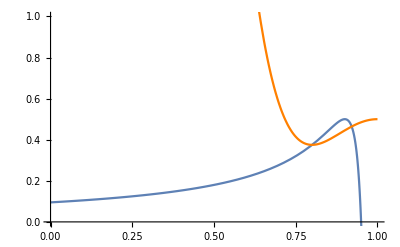

```mathematica
A = Plot[(√μ)/(√(s (-1+OverTilde[ma])^2))-(μ+(-μ+ν) OverTilde[ma])/(2 s (-1+OverTilde[ma])^2)/.ν->μ/.μ->10^-4/.s->0.01,{OverTilde[ma],0,1}];
B= Plot[μ/(μ+ν)-(μ OverTilde[ta] ((μ-ν) (μ+ν)^2+s μ ν OverTilde[ta]))/(μ+ν)^4-(μ OverTilde[ta]^2 (-(μ-ν)^2 (μ+ν)^4+s μ OverTilde[ta] ((μ-3 ν) (μ-ν) (μ+ν)^2+s μ (μ-2 ν) ν OverTilde[ta])))/(μ+ν)^7/.OverTilde[ta]->1-OverTilde[ma]/.ν->μ/.μ->10^-4/.s->0.01,{OverTilde[ma],0,1},PlotStyle->{Orange}];

Show[A,B, PlotRange->{0,1}]
```

The equilibrium is given by  1/OverTilde[ta]√(μ/s)-(μ+(ν-μ) OverTilde[ma])/(2 s OverTilde[ta]^2)+O(ϵ^3) when OverTilde[ta]<√(μ/s) and μ/(μ+ν)-(μ OverTilde[ta] ((μ-ν) (μ+ν)^2+s μ ν OverTilde[ta]))/(μ+ν)^4+O(ϵ^3) otherwise.

#### Case 2 : No dominance but the epigenetic allele can have different fitness from the mutant.

```mathematica
Case2Assump= {sAa->1/2(sAA+saa), sAb->1/2(sAA+sbb), sab->1/2(saa+sbb)};
Case2Fitness = {sAA->0}
```

{sAA→0}

```mathematica
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case2Assump/.Case2Fitness//FullSimplify
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef0+paef1 ϵ + paef2 ϵ^2+paef3 ϵ^3}/.SSWMApprox,{ϵ,0,3}]//FullSimplify;
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,1]==0,paef0],Assumptions->{0<OverTilde[ma]<1}]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,2]/.paef0->0//FullSimplify;
Solve[%==0,paef1]//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef0->0/.%[[1]]//FullSimplify;
Solve[%==0,paef2]//FullSimplify
```

((-1+paef) (2 μ+paef sbb (1+μ))+fa^2 paef^2 (saa-sbb) (μ-ν)+paef (2+sbb+paef sbb) ν+fa paef (sbb-paef sbb+2 μ+sbb μ-(2+sbb+2 paef sbb) ν+saa (-1+paef (1+μ+ν))))/(2 (1+fa paef (saa-sbb)+paef sbb))

{{paef0→0},{paef0→1}}

{{paef1→-(2 μ)/(saa+(-saa+sbb) OverTilde[ma])}}

{{paef2→(4 μ (-μ+(μ-ν) OverTilde[ma]))/(saa+(-saa+sbb) OverTilde[ma])^2}}

#### General Case

```mathematica
Case2Fitness = {sAA->0}
```

```mathematica
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case2Fitness//FullSimplify;
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef1 ϵ + paef2 ϵ^2}/.SSWMApprox,{ϵ,0,3}]//FullSimplify;
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,2]==0,paef1],Assumptions->{0<OverTilde[ma]<1}]/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef1->-μ/sAaeff//FullSimplify;
Solve[%==0,paef2]//FullSimplify;
%/.EffectiveFitness//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef0->0/.%[[1]]//FullSimplify;
```

{{paef1→-μ/sAaeff}}

{{paef2→(μ ((-saaeff+sAaeff) μ+sAaeff (μ-ν) OverTilde[ma]))/sAaeff^3}}

```mathematica
pAdiff=pAnext-pAef/.pAef->1-paef/.ChangeOfVariable/.Fitness/.Case2Fitness//FullSimplify;
pAdiffSeries = Series[%/.fa->fa0solSeries/.{paef->paef0+paef1 ϵ + paef2 ϵ^2}/.OverTilde[ma] ->1-OverTilde[ta]/.OverTilde[ta] ->OverTilde[ta] ϵ/.SSWMApprox,{ϵ,0,3}]//FullSimplify
FullSimplify[Solve[Coefficient[pAdiffSeries,ϵ,1]==0,paef0],Assumptions->{0<OverTilde[ma]<1}]//FullSimplify
Coefficient[pAdiffSeries,ϵ,2]/.paef0->0//FullSimplify
Solve[%==0,paef1]//FullSimplify
Coefficient[pAdiffSeries,ϵ,3]/.paef0->0/.%[[1]]//FullSimplify;
```

(-1+paef0) paef0 (sAb-2 paef0 sAb+paef0 sbb) ϵ+(-paef1 (sAb+6 (-1+paef0) paef0 sAb+(2-3 paef0) paef0 sbb)+(-1+paef0) (-paef0^2 (2 (-1+paef0) sAb-paef0 sbb) ((-1+2 paef0) sAb-paef0 sbb)+μ)+paef0 ν-(-1+paef0) paef0 ((-1+2 paef0) sAa+sAb-2 paef0 (sab+sAb-sbb)) OverTilde[ta]) ϵ^2+(-paef1^2 ((-3+6 paef0) sAb+sbb-3 paef0 sbb)-paef2 (sAb+6 (-1+paef0) paef0 sAb+(2-3 paef0) paef0 sbb)+(-1+paef0) paef0 ((-1+2 paef0) sAb-paef0 sbb) (-paef0^2 (-2 (-1+paef0) sAb+paef0 sbb)^2+μ+ν)+paef1 (paef0 (-4 (-1+paef0) (1+5 (-1+paef0) paef0) sAb^2+paef0 (9+4 paef0 (-7+5 paef0)) sAb sbb+(4-5 paef0) paef0^2 sbb^2)+μ+ν)+OverTilde[ta] (paef1 ((-1-6 (-1+paef0) paef0) sAa+sAb+6 paef0^2 (sab+sAb-sbb)+paef0 (-4 sab-6 sAb+4 sbb))+paef0 ((-1+paef0) paef0 (-4 (-1+paef0) (-1+2 paef0) sAa sAb+4 sAb^2-3 paef0 sAb (2 sab+4 sAb-3 sbb)+4 paef0^2 (sab+sAb-sbb) (2 sAb-sbb)+paef0 (-3+4 paef0) sAa sbb)+μ-ν)+(-1+paef0) paef0^2 (saa-2 sab+sbb) OverTilde[ta])) ϵ^3+O[ϵ]^4

{{paef0→0},{paef0→1},{paef0→sAb/(2 sAb-sbb)}}

-paef1 sAb-μ

{{paef1→-μ/sAb}}

### Paramutagenic Mutant/Paramutable Wildtype - A, B and a

#### Model

```mathematica
(*Selection*)
pAs = pA(pa wAa +pA wAA + pB wAB);
pas = pa(pa waa +pA wAa + pB waB);
pBs = pB (pa waB +pA wAB+ pB wBB);
(*Mutation*)
pAmut = pAs (1-μ)-mA (1-μ)(pa wAa+pB wAB)pA + μ pas +(1-ν)tA pBs ;
pamut = pas (1-μ) + μ pAs+ν pBs ;
pBmut = pBs (1-ν)(1-tA) + (1-μ)mA (pa wAa+pB wAB)pA  ;
(*Normalization*)
wavg = pamut + pAmut + pBmut; 
panext = pamut/wavg;
pAnext = pAmut/wavg; 
pBnext = pBmut/wavg;
```

```mathematica
Fitness = {wAA->1+sAA,wAa->1+sAa,waa->1+saa,wBB->1+sBB,wAB->1+sAB,waB->1+saB}; 
SSWMApprox = {sAA->sAA ϵ,sAa->sAa ϵ,saa->saa ϵ,sBB->sBB ϵ,sBb->sBb ϵ,sbb->sbb ϵ,sAB->sAB ϵ,sAb->sAb ϵ,saB->saB ϵ,sab->sab ϵ,μ->μ ϵ^2, ν->ν ϵ^2,s->s ϵ}; 
ChangeOfVariable = {pa->1-pAef, pA->fA pAef,pB->(1-fA) pAef};
EffectiveFitness = {sAA->(sAAeff-(2 OverTilde[mA] (1-OverTilde[mA] )sAB + OverTilde[mA]^2 sBB ))/(1-OverTilde[mA] )^2, saB->(sAaeff -(1-OverTilde[mA] )sAa )/OverTilde[mA]  };
```

#### The QEE

```mathematica
fAnext = pAnext/pAef//FullSimplify;
%/.ChangeOfVariable//FullSimplify;
fADiffSeries = Series[%-fA/.Fitness/.SSWMApprox/.{fA->fA0+fA1 ϵ},{ϵ,0,0}]//FullSimplify;
fA0sol=Solve[Coefficient[fADiffSeries,ϵ,0]==0,fA0]//FullSimplify;
(Numerator[fA0/.fA0sol])/(mA+tA)/.{mA->OverTilde[mA](mA+tA),tA->(1-OverTilde[mA])(mA+tA)};
fA0solsim=FullSimplify[%,Assumptions->{mA+tA>0}]/(2 OverTilde[mA] pAef)
fA0solSerieslesshalf = Normal[FullSimplify[Series[fA0solsim[[1]]/.pAef->1-pa ϵ, {ϵ,0,1}],Assumptions->{0<OverTilde[mA]<1/2}]]/.ϵ->1
fA0solSeriesgreaterhalf = Normal[FullSimplify[Series[fA0solsim[[1]]/.pAef->1-pa ϵ, {ϵ,0,1}],Assumptions->{1/2<OverTilde[mA]<1}]]/.ϵ->1
fA0solSeries =  Normal[FullSimplify[Series[fA0solsim[[1]] , {OverTilde[mA],1/2,1}]]]
fA0solSerieshalf =  Normal[FullSimplify[Series[%/.pAef->1-pa τ, {τ,0,1}], Assumptions->{1>mA>0}]]/.τ->1//FullSimplify
Series[fA0solsim/.OverTilde[mA]->1 - OverTilde[tA] ϵ/.pAef ->1-paef ϵ,{ϵ,0,2}]//FullSimplify
```

{(1-√(1+4 pAef (-1+OverTilde[mA]) OverTilde[mA]))/(2 pAef OverTilde[mA]),(1+√(1+4 pAef (-1+OverTilde[mA]) OverTilde[mA]))/(2 pAef OverTilde[mA])}

1+(pa OverTilde[mA])/(-1+2 OverTilde[mA])

-1+1/OverTilde[mA]-(pa (-1+OverTilde[mA])^2)/(OverTilde[mA] (-1+2 OverTilde[mA]))

1/(1+√(1-pAef))+(2 (-1+√(1-pAef)) (-1/2+OverTilde[mA]))/pAef

-2 (1-√pa+pa) (-1+OverTilde[mA])

{OverTilde[tA] ϵ+OverTilde[tA]^2 ϵ^2+O[ϵ]^3,1+paef ϵ+paef (paef+OverTilde[tA]) ϵ^2+O[ϵ]^3}

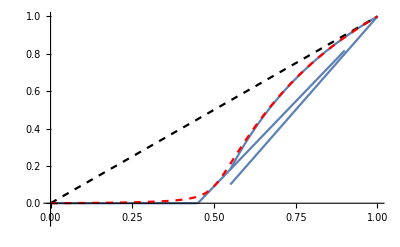

```mathematica
P1= Plot[0/.pa->0.01,{OverTilde[mA],0,0.45}, PlotRange->{0,1}];
P2=Plot[1-(-2 (1-√pa+pa) (-1+OverTilde[mA]))/.pa->0.01,{OverTilde[mA],0.45,0.9}];
P3=Plot[2-1/OverTilde[mA]/.pa->0.01,{OverTilde[mA],0.55,1}];
P5=Plot[1-2(1-OverTilde[mA])/.pa->0.01,{OverTilde[mA],0.55,1}];
P4=Plot[x,{x,0,1},PlotStyle->{Black,Dashed}];
P6 = Plot[1-(1-√(1+4 pAef (-1+OverTilde[mA]) OverTilde[mA]))/(2 pAef OverTilde[mA])/.pAef->0.99,{OverTilde[mA],0,1},PlotStyle->{Red,Dashed}];
Show[P1,P2,P3,P4,P5,P6, PlotRange->{{0,1},{-0.1,1}}]
```

#### Case 1 : Epigenetically modified allele has the same fitness' as the other genetic allele .

```mathematica
Case1Assump= {sBB->saa, saB->saa, sAB->sAa};
Case1Fitness = {sAA->0,sAa-> -h s, saa-> -s};
```

Case 1 a : h != 0 (Non - recessive mutant)

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
padiffSeries = Series[%/.fA->fA0solSerieslesshalf/.pAef->1-pa/.{pa->pa0+pa1 ϵ}/.SSWMApprox,{ϵ,0,2}]//FullSimplify;
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,1]==0,pa0],Assumptions->{0<OverTilde[mA]<1/2}]/.EffectiveFitness//FullSimplify
Coefficient[padiffSeries,ϵ,2]/.pa0->0//FullSimplify;
Solve[%==0,pa1]/.EffectiveFitness//FullSimplify
(*Coefficient[pAdiffSeries,ϵ,3]/.paef0->0/.%[[1]]//FullSimplify;
Solve[%==0,paef2]/.EffectiveFitness//FullSimplify*)
```

{{pa0→0},{pa0→1},{pa0→-2+1/OverTilde[mA]},{pa0→(-1+2 h+OverTilde[mA]-2 h OverTilde[mA]-√((-1+2 h) (-1+2 h+OverTilde[mA] (2-8 h+(-1+10 h) OverTilde[mA]))))/(2 (-1+2 h) OverTilde[mA])},{pa0→(-1+2 h+OverTilde[mA]-2 h OverTilde[mA]+√((-1+2 h) (-1+2 h+OverTilde[mA] (2-8 h+(-1+10 h) OverTilde[mA]))))/(2 (-1+2 h) OverTilde[mA])}}

{{pa1→μ/(h s)}}

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
padiffSeries = Series[%/.fA->fA0solSeriesgreaterhalf/.pAef->1-pa/.{pa->pa0+pa1 ϵ }/.SSWMApprox,{ϵ,0,2}]//FullSimplify;
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,1]==0,pa0],Assumptions->{1/2<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
Coefficient[padiffSeries,ϵ,2]/.pa0->0//FullSimplify;
Solve[%==0,pa1]/.EffectiveFitness//FullSimplify
```

{{pa0→0},{pa0→1},{pa0→-2+1/(1-OverTilde[mA])},{pa0→(OverTilde[mA]-2 h OverTilde[mA]-√((-1+2 h) (-4+8 h+OverTilde[mA] (16-28 h+(-17+26 h) OverTilde[mA]))))/(2 (-1+2 h) (-1+OverTilde[mA]))},{pa0→(OverTilde[mA]-2 h OverTilde[mA]+√((-1+2 h) (-4+8 h+OverTilde[mA] (16-28 h+(-17+26 h) OverTilde[mA]))))/(2 (-1+2 h) (-1+OverTilde[mA]))}}

{{pa1→-(OverTilde[mA] (-μ+ν+(μ-2 ν) OverTilde[mA]))/(s (-1+OverTilde[mA]) (1-2 h+(-2+3 h) OverTilde[mA]))}}

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify;
padiffSeries = Series[%/.fA->fA0solSerieshalf/.pAef->1-pa/.{pa->pa1 ϵ}/.SSWMApprox,{ϵ,0,2}]//FullSimplify
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,1]==0,pa0],Assumptions->{0<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
Coefficient[padiffSeries,ϵ,2]/.pa0->0//FullSimplify;
Solve[%==0,pa1]/.EffectiveFitness//FullSimplify
```

(ν-2 ((-1+h) pa1 s+μ-ν) (-1+OverTilde[mA])+4 (pa1-2 h pa1) s (-1+OverTilde[mA])^2) ϵ^2+O[ϵ]^(5/2)

{{}}

{{pa1→-(-2 μ+ν+2 (μ-ν) OverTilde[mA])/(2 s (-1+OverTilde[mA]) (1-3 h+(-2+4 h) OverTilde[mA]))}}

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness//FullSimplify
padiffSeries = Series[%/.fA->fA0solSeriesgreaterhalf/.pAef->1-pa/.{pa->pa0+pa1 ϵ}/.OverTilde[mA]->1-OverTilde[tA] ϵ/.SSWMApprox,{ϵ,0,3}]//FullSimplify
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa0],Assumptions->{0<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
Coefficient[padiffSeries,ϵ,3]/.pa0->ν/(ν+μ);
FullSimplify[Solve[%==0,pa1],Assumptions->{0<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
```

(-((-1+s) ((-1+pAef) μ+pAef ν))+fA^2 pAef^2 s (1-pAef-ν+h (-2+2 pAef+μ+ν))+fA pAef (μ-ν+s (h+(-1+pAef) (1+μ)+(1+pAef) ν-h pAef (1+μ+ν))))/(1+(-1+fA pAef) (1+fA (-1+2 h) pAef) s)

(ν-pa0 (μ+ν)+pa0 (-1+h+pa0-h pa0) s OverTilde[tA]) ϵ^2+(-pa1 (μ+ν)+OverTilde[tA] ((-1+h+2 pa0-2 h pa0) pa1 s-(-1+pa0) ((-1+h) pa0 s^2+μ-ν)-h (-1+pa0)^2 pa0 s OverTilde[tA])) ϵ^3+O[ϵ]^4

{{pa0→-(μ+ν+s OverTilde[tA]-h s OverTilde[tA]-√(4 (-1+h) s ν OverTilde[tA]+(μ+ν+(s-h s) OverTilde[tA])^2))/(2 (-1+h) s OverTilde[tA])},{pa0→-(μ+ν+s OverTilde[tA]-h s OverTilde[tA]+√(4 (-1+h) s ν OverTilde[tA]+(μ+ν+(s-h s) OverTilde[tA])^2))/(2 (-1+h) s OverTilde[tA])}}

{{pa1→(μ OverTilde[tA] ((μ+ν) (μ^2+((-1+h) s^2-ν) ν)-h s μ ν OverTilde[tA]))/((μ+ν)^4-(-1+h) s (μ-ν) (μ+ν)^2 OverTilde[tA])}}

```mathematica
A1 = Plot[μ/(h s)/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[mA],0,1/2},PlotStyle->{Blue}];
A2 = Plot[(μ OverTilde[mA]^2)/(s (-1+OverTilde[mA]) (1-2 h+(-2+3 h) OverTilde[mA]))/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[mA],1/2,1},PlotStyle->{Blue}];
B= Plot[(-2 μ+(-1+h) s OverTilde[ta]+√(4 μ^2+(-1+h)^2 s^2 OverTilde[ta]^2))/(2 (-1+h) s OverTilde[ta])/.OverTilde[ta]->1-OverTilde[mA]/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[mA],0,1},PlotStyle->{Orange}];
```

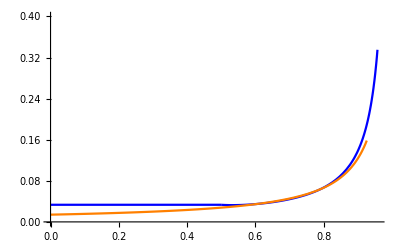

```mathematica
Show[A1,A2,B,PlotRange->{0,0.4}]
```

Case 1 a : h = 0 (Recessive mutant)

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness/.h->0//FullSimplify;
padiffSeries = FullSimplify[Series[%/.fA->fA0solSerieslesshalf/.pAef->1-pa/.{pa->pa1 ϵ^(1/2)}/.SSWMApprox,{ϵ,0,2}],Assumptions->{0<OverTilde[mA]<1/2}];
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa1],Assumptions->{0<OverTilde[mA]<1/2}]/.EffectiveFitness//FullSimplify
```

{{pa1→-(√μ)/(√((s (-1+OverTilde[mA]))/(-1+2 OverTilde[mA])))},{pa1→(√μ)/(√((s (-1+OverTilde[mA]))/(-1+2 OverTilde[mA])))}}

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness/.h->0//FullSimplify;
padiffSeries = FullSimplify[Series[%/.fA->fA0solSeriesgreaterhalf/.pAef->1-pa/.{pa->pa1 ϵ}/.SSWMApprox,{ϵ,0,2}],Assumptions->{1/2<OverTilde[mA]<1}]
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa1],Assumptions->{1/2<OverTilde[mA]<1}]/.EffectiveFitness//Factor
```

(ν+pa1 s (-1+1/OverTilde[mA])^2+((pa1 s-μ+ν) (-1+OverTilde[mA]))/OverTilde[mA]) ϵ^2+O[ϵ]^3

{{pa1→(OverTilde[mA] (-μ+ν+μ OverTilde[mA]-2 ν OverTilde[mA]))/(s (-1+OverTilde[mA]) (-1+2 OverTilde[mA]))}}

(OverTilde[mA] (μ OverTilde[tA]+(2 OverTilde[mA]-1)ν))/(s OverTilde[tA] (2 OverTilde[mA]-1))

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness/.fA->(1-√(1+4 pAef (-1+OverTilde[mA]) OverTilde[mA]))/(2 pAef OverTilde[mA])/.pAef->1-pa//FullSimplify
padiffSeries = FullSimplify[Series[%/.{pa->pa1 ϵ}/.OverTilde[mA]->0.5+ϵ/.SSWMApprox/.h->0,{ϵ,0,2}]]
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa1]]/.EffectiveFitness//Factor
```

(2 ((-1+2 h) pa^2 s+ν-2 s ν+h s (μ+ν)-pa (μ+ν+s (-1-μ-2 ν+h (2+μ+ν)))) OverTilde[mA]^2+s ((-1+2 h) pa+ν-h (μ+ν)) (-1+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))+OverTilde[mA] (2 (1-2 h) pa^2 s+μ-ν-μ √(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA])+h s (μ+ν) (-3+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))+ν (√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA])-2 s (-2+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA])))+pa s ((1+ν) (-3+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))+μ (-1+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))-h (-5+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA])+μ (-3+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))+ν (-3+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))))))/((2+2 (-2+2 h+pa-2 h pa) s) OverTilde[mA]^2-(-1+2 h) s (-1+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))+2 s OverTilde[mA] (2-pa-√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA])+h (-3+2 pa+√(1-4 (-1+pa) (-1+OverTilde[mA]) OverTilde[mA]))))

1. μ ϵ^2+O[ϵ]^(5/2)

{}

```mathematica
\ff
```

```mathematica
padiff//FullSimplify
Solve[%== 0, pa]
```

-(pa^2 s+μ+√pa (-μ+ν)+pa^(3/2) s (-1+μ+ν)-pa (μ+ν+s ν))/(-1+pa s)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case1Assump/.Case1Fitness/.h->0//FullSimplify
padiffSeries = Series[%/.fA->fA0solSeriesgreaterhalf/.pAef->1-pa/.{pa->pa0+pa1 ϵ}/.OverTilde[mA]->1-OverTilde[tA] ϵ/.SSWMApprox,{ϵ,0,3}]//FullSimplify
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa0],Assumptions->{0<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
Coefficient[padiffSeries,ϵ,3]/.pa0->ν/(ν+μ);
FullSimplify[Solve[%==0,pa1],Assumptions->{0<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
```

(fA^2 pAef^2 s (-1+pAef+ν)+(-1+s) ((-1+pAef) μ+pAef ν)-fA pAef (μ+(-1+pAef) s (1+μ)-ν+(1+pAef) s ν))/(-1+(-1+fA pAef)^2 s)

(ν-pa0 (μ+ν)+(-1+pa0) pa0 s OverTilde[tA]) ϵ^2+(-pa1 (μ+ν)+((-1+2 pa0) pa1 s+(-1+pa0) (pa0 s^2-μ+ν)) OverTilde[tA]) ϵ^3+O[ϵ]^4

{{pa0→(μ+ν+s OverTilde[tA]-√(-4 s ν OverTilde[tA]+(μ+ν+s OverTilde[tA])^2))/(2 s OverTilde[tA])},{pa0→(μ+ν+s OverTilde[tA]+√(-4 s ν OverTilde[tA]+(μ+ν+s OverTilde[tA])^2))/(2 s OverTilde[tA])}}

{{pa1→(μ (μ^2-ν (s^2+ν)) OverTilde[tA])/((μ+ν)^3+s (μ-ν) (μ+ν) OverTilde[tA])}}

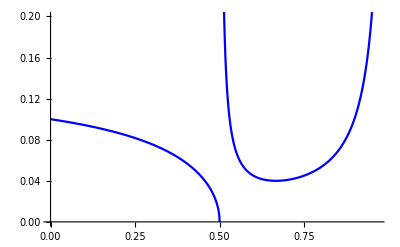

```mathematica
A1 = Plot[(√(μ-2 μ OverTilde[mA]))/(√(s-s OverTilde[mA]))/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[mA],0,1/2},PlotStyle->{Blue}];
A2 = Plot[(OverTilde[mA] (-μ+ν+μ OverTilde[mA]-2 ν OverTilde[mA]))/(s (-1+OverTilde[mA]) (-1+2 OverTilde[mA]))/.ν->10^-4/.μ->10^-4/.s->0.01/.h->0.3,{OverTilde[mA],1/2 ,1},PlotStyle->{Blue}];

Show[A1,A2, PlotRange->{0,0.2}]
```

#### Case 2 : No dominance but the epigenetic allele can have different fitness from the mutant .

```mathematica
Case2Assump= {sAa->1/2(sAA+saa), sAB->1/2(sAA+sBB), saB->1/2(saa+sBB)};
Case2Fitness = {sAA->0}
```

{sAA→0}

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case2Assump/.Case2Fitness/.pAef->1-pa//FullSimplify;
padiffSeries = FullSimplify[Series[%/.fA->fA0solSeries/.pAef->1-pa/.{pa->pa1 ϵ }/.SSWMApprox,{ϵ,0,2}],Assumptions->{0<OverTilde[mA]<1/2}];
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa1],Assumptions->{0<OverTilde[mA]<1/2}]/.EffectiveFitness//FullSimplify
```

{{pa1→-(2 μ)/saa}}

```mathematica
padiff=panext-pa/.ChangeOfVariable/.Fitness/.Case2Assump/.Case2Fitness/.pAef->1-pa//FullSimplify;
padiffSeries = FullSimplify[Series[%/.fA->fA0solSeries/.pAef->1-pa/.{pa->pa1 ϵ }/.SSWMApprox,{ϵ,0,2}],Assumptions->{1/2<OverTilde[mA]<1}];
FullSimplify[Solve[Coefficient[padiffSeries,ϵ,2]==0,pa1],Assumptions->{1/2<OverTilde[mA]<1}]/.EffectiveFitness//FullSimplify
```

{{pa1→(2 (-μ+ν+(μ-2 ν) OverTilde[mA]))/(sBB+(saa-2 sBB) OverTilde[mA])}}

## Diploid - Classic

```mathematica
(*Selection*)
pas = pa (pA wAa +pa waa );
pAs = pA (pA wAA +pa wAa );

(*Mutation*)
pamut = pas (1-ν) + μ pAs  ;
pAmut = pAs (1-μ) +ν pas ;

(*Normalization*)
wavg = pamut + pAmut ; 
panext = pamut/wavg;
pAnext = pAmut/wavg;
recursions = panext/.pA->1-pa;
```

```mathematica
fitness = {wAA->1+sAA,wAa ->1+sAa,waa->1+saa};
SSWM = {sAA->sAA ϵ, sAa->sAa ϵ, saa->saa ϵ, μ->μ ϵ^2,ν->ν ϵ^2};
padiffseries = Series[recursions-pa/.fitness/.SSWM/.pa->pa0+pa1 ϵ+pa2 ϵ^2,{ϵ,0,3}]//FullSimplify;
pa0sol = Solve[Coefficient[padiffseries,ϵ,1]==0,pa0]
Coefficient[padiffseries,ϵ,2]/.pa0sol[[1]]
pa1sol = Solve[%==0,pa1]
Coefficient[padiffseries,ϵ,3]/.pa0sol[[1]]/.pa1sol[[1]]
pa1sol = Solve[%==0,pa2]//Factor
```

{{pa0→0},{pa0→1},{pa0→(-sAa+sAA)/(saa-2 sAa+sAA)}}

pa1 sAa-pa1 sAA+μ

{{pa1→-μ/(sAa-sAA)}}

pa2 sAa+(saa μ^2)/(sAa-sAA)^2-(sAa μ^2)/(sAa-sAA)^2-(μ (sAA^2+2 μ))/(sAa-sAA)+μ (sAA+μ/(sAa-sAA))-sAA (pa2+μ-(sAa μ)/(sAa-sAA))+(μ ν)/(sAa-sAA)

{{pa2→-(μ (sAa^2 sAA-2 sAa sAA^2+sAA^3+saa μ-2 sAa μ+sAA μ+sAa ν-sAA ν))/(sAa-sAA)^3}}

## Evolutionary Rescue - Pure Epigenetics

```mathematica
Wavg = 1-r+fB s
fBnext = ((1-t)fB(1-r+s)+m(1-fB)(1-r) )/Wavg
fBseries = Series[fBnext-fB/.{r->r ϵ,s->s ϵ,fB->fB0+fB1 ϵ},{ϵ,0,2}]//FullSimplify
Solve[Coefficient[fBseries,ϵ,0]==0,fB0]
Coefficient[fBseries,ϵ,1]/.fB0->m/(m+t)//FullSimplify
Solve[%==0,fB1]
```

1-r+fB s

((1-fB) m (1-r)+fB (1-r+s) (1-t))/(1-r+fB s)

(m-fB0 m-fB0 t)+((-1+fB0) fB0 s (-1+m+t)-fB1 (m+t)) ϵ-s (fB1-2 fB0 fB1+(-1+fB0) fB0 (-r+fB0 s)) (-1+m+t) ϵ^2+O[ϵ]^3

{{fB0→m/(m+t)}}

-(m s t (-1+m+t))/(m+t)^2-fB1 (m+t)

{{fB1→-(m s t (-1+m+t))/(m+t)^3}}

```mathematica
fB->fB0+fB1/.fB0->m/(m+t)/.fB1->-(m (2 m r-2 m s+2 r t-s t+m s t+s t^2))/(m+t)^3/.m->r/s tot/.t->(1-r/s)tot//FullSimplify
```

fB→(r (s+r (-1+tot)+tot-s tot))/(s tot)

```mathematica
fB->fB0+fB1/.fB0->m/(m+t)/.fB1->-(m s t (-1+m+t))/(m+t)^3/.m->r/s tot/.t->(1-r/s)tot//FullSimplify
```

fB→(r (s+r (-1+tot)+tot-s tot))/(s tot)

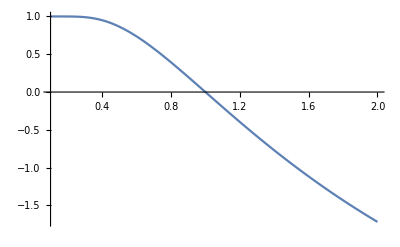

```mathematica
A = Plot[1-Exp[-2(-r+fB s)N]/.fB->fB0+fB1/.fB0->m/(m+t)/.fB1->-(m (2 m r-2 m s+2 r t-s t+m s t+s t^2))/(m+t)^3/.m->r/s tot/.t->(1-r/s)tot/.r->0.01/.s->0.02/.N->10000,{tot,0.1,2}];
B =Plot[0,{x,0.1,1}];
Show[A]
```